## Goal

Given any input state, classify it into:

- dies out
- contains multiple solutions
- periodic without shift
- periodic with shift s
- aperiodic (e.g. glider gun)

The DetectPeriod[list] function, when given an initial state, returns an association with the period, canonical representation (i.e. smallest reachable state that gives that same solution), and shift.

## Implementation

### Helper Functions

```mathematica
RunCode20[init_, steps_]:=CellularAutomaton[{20, {2, 1}, 2}, {init, 0}, steps]
```

```mathematica
CellularAutomaton[{20, {2, 1}, 2}, {init, 0}, steps]
```

```mathematica
StripZeros=FunctionCompile[Function[Typed[list, "PackedArray"::["MachineInteger", 1]],Module[
{i=1, j=Length[list]},
If[Max[list]==0, Return[Table[0, {iter, 0}]]];
While[list[[i]]==0, i++];
 While[list[[j]]==0, j--]; 
list[[i;;j]]
]], CompilerOptions->{"LLVMOptimization"->"ClangOptimization"[3], "AbortHandling"->False, "OptimizationLevel"->3,"InvocationMode"->"Standalone"}];

RepeatedTiming[StripZeros[RandomInteger[{0, 1}, 1000]]]//First
StripZeros[{0, 0, 0, 0,0}]
```

1.79545×10^-6

{}

```mathematica
MaxGapLength=FunctionCompile[Function[Typed[list, "PackedArray"::["MachineInteger", 1]],Module[
{currentlen=0, maxlen=0},
Do[currentlen=If[i==0, currentlen+1,0]; maxlen=Max[maxlen, currentlen];, {i,list}];
maxlen
]], CompilerOptions->{"LLVMOptimization"->"ClangOptimization"[3], "AbortHandling"->False, "OptimizationLevel"->3,"InvocationMode"->"Standalone"}];
RepeatedTiming[MaxGapLength[RandomInteger[{0, 1}, 1000]]]
```

{3.71411×10^-6,9}

```mathematica
FindRepeatDeterministic[list_]:=
list[[-First[FirstPosition[Reverse[list[[;;-2]]], list[[-1]], {0}]];;]]
```

```mathematica
SplitSeparateSolutions[carun_, radius_:1]:=Module[{mask, mc, colors, carunpadded},
carunpadded=ArrayPad[#, 1]&/@carun;
mask=carunpadded[[All, 1;;-3]]+carunpadded[[All, 2;;-2]]+carunpadded[[All, 3;;-1]];
mc=Last[MorphologicalComponents[Image[mask], CornerNeighbors->False]];
colors=Union[mc];
Table[(1-Unitize[c-mc])*carun[[-1]], {c, colors}]/.{0...}->Nothing
]
SplitSeparateSolutions[RunCode20[IntegerDigits[233 + 2^14 * 151, 2], 100]]
SplitSeparateSolutions[RunCode20[IntegerDigits[12555286547204781505564672, 2], 100]]
First@RepeatedTiming[SplitSeparateSolutions[RunCode20[IntegerDigits[12555286547204781505564672, 2], 100]]]
```

{{1,0,0,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,0,0,1}}

{{1,0,0,1,1,0,0,0,0,1,0,1,1,0,1,1,0,0,0,1,0,1,0,0,1,0,0,1,0,0,1,0,0,0,1,1,1,1,1,0,0,1,1,1,1,1,1,0,0,0,1,1,1,1,1,1,0,0,1,0,1,1,0,1,1,1,1,0,1,1,1,1,0}}

0.000733913

### Detect Period

```mathematica
Clear[DetectPeriod]
DetectPeriod[rule_, init_, steps_:120, maxdepth_:5]:=Module[
{carun, frd, separatesolutions, period, canonical, shift},
If[maxdepth<=0,
(*Print["Possible Glider Gun: ", FromDigits[init, rule[[2, 1]]]];*)
Return[{<|"Period"->0, "Canonical"->FromDigits[init, rule[[2, 1]]], "Shift"->0, "IsGliderGun"->True|>}];
];
carun = CellularAutomaton[rule, {init, 0}, steps];
(* If it dies, return *);
If[Max[carun[[-1]]]==0, Return[{}]];

(* Detect Periodicity *)
frd=FindRepeatDeterministic[StripZeros/@carun];

(* If unfinished and probably unseparated, recurse with more steps *);
If[Length[frd]==0, 
Return[If[MaxGapLength[carun[[-1]]]>5,
separatesolutions=SplitSeparateSolutions[carun];
Join@@Table[
DetectPeriod[rule, subsolution, steps, maxdepth-1],
 {subsolution, separatesolutions}
],
DetectPeriod[rule, carun[[-1]], 2 * steps, maxdepth - 1]
]]
];

(* Otherwise, run again for pure periodicity *)
carun=CellularAutomaton[rule, {carun[[-1]], 0}, steps];

(* If it's multiperiodic, split solutions *);
separatesolutions=SplitSeparateSolutions[carun];
separatesolutions=SortBy[separatesolutions,First[FirstPosition[#, 1, 0]]&];

(* Recurse on each subsolution, if they exist *);
If[Length[separatesolutions]>1,
Return[Join@@Table[
DetectPeriod[rule, subsolution, steps, maxdepth-1],
 {subsolution, separatesolutions}
]]
];

(* Return single-solution period *);
period=Length[frd];
canonical=Min[Min[FromDigits[StripZeros[#],rule[[2, 1]]]&/@frd], Min[FromDigits[StripZeros[Reverse[#]],rule[[2, 1]]]&/@frd]];
carun=CellularAutomaton[rule, {IntegerDigits[canonical, rule[[2, 1]]], 0}, period];
If[Max[Last[carun]]==0, Print["here"];Return[{}]];
shift=Log[rule[[2, 1]], FromDigits[First[carun], rule[[2, 1]]]/FromDigits[Last[carun], rule[[2, 1]]]];
Return[{<|"Period"->period,"Canonical"->canonical, "Shift"->shift|>}];
]
```

```mathematica
{n, k, r}
```

```mathematica
{20, {2, 1}, 2}
```

### Small-Scale Testing

```mathematica
list=;
DetectPeriod[list]

list=;
DetectPeriod[list]

list=;
DetectPeriod[list]
```

{<|Period→2,Canonical→151,Shift→0|>,<|Period→2,Canonical→151,Shift→0|>}

{<|Period→10,Canonical→360759087837221,Shift→0|>,<|Period→10,Canonical→360759087837221,Shift→0|>}

{<|Period→10,Canonical→360759087837221,Shift→0|>,<|Period→9,Canonical→187,Shift→1|>}

```mathematica
foundsolutions=Normal[ResourceData["Persistent Structures in the Code 20 Cellular Automaton"]][[All, "Number"]]

d1=Table[First[DetectPeriod[IntegerDigits[s, 2]]], {s, foundsolutions}][[All, "Period"]]
d2=Normal[ResourceData["Persistent Structures in the Code 20 Cellular Automaton"]][[All, "Period"]]
d1==d2

d1=Table[First[DetectPeriod[IntegerDigits[s, 2]]], {s, foundsolutions}][[All, "Shift"]]
d2=Normal[ResourceData["Persistent Structures in the Code 20 Cellular Automaton"]][[All, "Shift"]]
Abs[d1]==Abs[d2]
```

{151,187,189,195,221,635,889,125231,595703,610999,14871103,16537415,256296063,22503642597,222678959859,10495070598767,360759087837221,2197520782601119,11221488970893447375,142082121178470981231}

{2,9,1,22,9,1,1,38,4,4,2,2,5,5,3,8,10,10,6,10}

{2,9,1,22,9,1,1,38,4,4,2,2,5,5,3,8,10,10,6,10}

True

{0,1,0,0,1,1,1,0,0,0,1,1,0,0,0,0,0,0,0,0}

{0,1,0,0,-1,1,-1,0,0,0,1,-1,0,0,0,0,0,0,0,0}

True

## Testing and Large Scale Search

```mathematica
list=;
ArrayPlot[RunCode20[list, 100]]
DetectPeriod[list]//Column
```

-Graphics-

<|Period→2,Canonical→151,Shift→0|>
<|Period→2,Canonical→151,Shift→0|>
<|Period→9,Canonical→187,Shift→1|>

```mathematica
(* Find all solutions with periods that aren't easy to find *)
numtosearch=1000;
initwidth=100;
easysolutionperiods={0, 1, 2};  (* include 9 and 22, then 4 and 38 for longer searches *)


easysolutionperiods=Dispatch[Append[#->True&/@easysolutionperiods, _->False]];

found=ParallelTable[If[AllTrue[DetectPeriod[#][[All, "Period"]], elem|->elem/.easysolutionperiods],Nothing,#]&[RandomInteger[{0, 1}, initwidth]], {i, numtosearch}];

ParallelTable[
Labeled[ArrayPlot[RunCode20[sol, 200]], ClickToCopy[Values@DetectPeriod[sol], sol]],{sol, found}]
```

#### Large Solution Search:

```mathematica
(* Find all solutions with periods that aren't easy to find *)
numtosearch=1000000;
initwidth=300;
easysolutionperiods={0, 1, 2, 4, 9, 22, 38};  (* include 9 and 22, then 4 and 38 for longer searches *)


easysolutionperiods=Dispatch[Append[#->True&/@easysolutionperiods, _->False]];

found=ParallelTable[If[AllTrue[DetectPeriod[#][[All, "Period"]], elem|->elem/.easysolutionperiods],Nothing,#]&[RandomInteger[{0, 1}, initwidth]], {i, numtosearch}];

ParallelTable[
Labeled[ArrayPlot[RunCode20[sol, 200]], ClickToCopy[Values@DetectPeriod[sol], sol]],{sol, found}]
```

### Testing on Code 20

```mathematica
list=;
ArrayPlot[RunCode20[list, 100]]
DetectPeriod[list]//Column
```

-Graphics-

<|Period→2,Canonical→151,Shift→0|>
<|Period→2,Canonical→151,Shift→0|>
<|Period→9,Canonical→187,Shift→1|>

```mathematica
list=;
```

```mathematica
ArrayPlot[RunCode20[list, 100]]
```

-Graphics-

```mathematica
DetectPeriod[{20, {2, 1}, 2},list]//Column
```

<|Period→2,Canonical→151,Shift→0|>
<|Period→2,Canonical→151,Shift→0|>
<|Period→9,Canonical→187,Shift→1|>

### Code 1309

```mathematica
ArrayPlot[CellularAutomaton[{1329, {3, 1}, 2} , {list, 0}, 100]]
```

-Graphics-

```mathematica
ArrayPlot[CellularAutomaton[{1329, {3, 1}, 2} , {RandomInteger[2, 100], 0}, 100]]
```

-Graphics-

```mathematica
ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[#, 3], 0}, 1000]]&/@ {54889,97439,166426}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
DetectPeriod[{1329,{3,1},1},IntegerDigits[54889, 3], 100]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

{<|Period→78,Canonical→9571,Shift→∞|>,<|Period→78,Canonical→9571,Shift→∞|>,<|Period→78,Canonical→9571,Shift→∞|>,<|Period→78,Canonical→9571,Shift→∞|>,<|Period→78,Canonical→9571,Shift→∞|>,<|Period→78,Canonical→9571,Shift→∞|>,<|Period→78,Canonical→9571,Shift→∞|>,<|Period→78,Canonical→9571,Shift→∞|>,<|Period→78,Canonical→9571,Shift→∞|>,<|Period→78,Canonical→9571,Shift→∞|>,<|Period→78,Canonical→9571,Shift→∞|>,<|Period→78,Canonical→9571,Shift→∞|>,<|Period→78,Canonical→9571,Shift→∞|>,<|Period→0,Canonical→2005018347831839992202108621675104590236708235790110521669090716796960709569725947280297834586275330630741,Shift→0,IsGliderGun→True|>,<|Period→0,Canonical→1698756896703125527731443196314833767303177842115039467968715045981549566099205516401941252930482771876870826285794811,Shift→0,IsGliderGun→True|>,<|Period→78,Canonical→9571,Shift→∞|>,<|Period→78,Canonical→9571,Shift→∞|>,<|Period→78,Canonical→9571,Shift→∞|>,<|Period→78,Canonical→9571,Shift→∞|>,<|Period→78,Canonical→9571,Shift→∞|>,<|Period→78,Canonical→9571,Shift→∞|>,<|Period→78,Canonical→9571,Shift→∞|>}

```mathematica
FromDigits[{0,0,0,0,0,0,2,2,0,0,1,0,2,0,2,2,2,0,2,0,1,0,0,2,2,0,0},{1329,{3,1},1}⟦2,1⟧]
```

9352253592

```mathematica
ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[9352253592, 3], 0}, 200]]
```

-Graphics-

```mathematica
(If[5≤0,Return[{Association["Period"->0,"Canonical"->FromDigits[{0,0,0,0,0,0,2,2,0,0,1,0,2,0,2,2,2,0,2,0,1,0,0,2,2,0,0},{1329,{3,1},1}⟦2,1⟧],"Shift"->0,"IsGliderGun"->True]}];];carun$447262=CellularAutomaton[{1329,{3,1},1},{{0,0,0,0,0,0,2,2,0,0,1,0,2,0,2,2,2,0,2,0,1,0,0,2,2,0,0},0},120])
```

{{0,0,2,2,0,0,1,0,2,0,2,2,2,0,2,0,1,0,0,2,2,0,0},{0,0,1,1,0,2,2,1,0,1,1,1,1,1,0,1,2,2,0,1,1,0,0},{0,2,0,0,1,1,2,1,0,0,1,1,1,0,0,1,2,1,1,0,0,2,0},{0,0,0,2,0,1,1,1,2,2,0,1,0,2,2,1,1,1,0,2,0,0,0},{0,0,0,0,1,0,1,1,2,1,1,2,1,1,2,1,1,0,1,0,0,0,0},{0,0,0,2,2,0,0,1,1,1,1,1,1,1,1,1,0,0,2,2,0,0,0},{0,0,0,1,1,0,2,0,1,1,1,1,1,1,1,0,2,0,1,1,0,0,0},{0,0,2,0,0,1,0,1,0,1,1,1,1,1,0,1,0,1,0,0,2,0,0},{0,0,0,0,2,2,0,2,0,0,1,1,1,0,0,2,0,2,2,0,0,0,0},{0,0,0,0,1,1,1,0,0,2,0,1,0,2,0,0,1,1,1,0,0,0,0},{0,0,0,2,0,1,0,2,0,0,1,2,1,0,0,2,0,1,0,2,0,0,0},{0,0,0,0,1,2,1,0,0,2,1,1,1,2,0,0,1,2,1,0,0,0,0},{0,0,0,2,1,1,1,2,0,1,1,1,1,1,0,2,1,1,1,2,0,0,0},{0,0,0,1,1,1,1,1,1,0,1,1,1,0,1,1,1,1,1,1,0,0,0},{0,0,2,0,1,1,1,1,0,0,0,1,0,0,0,1,1,1,1,0,2,0,0},{0,0,0,1,0,1,1,0,2,0,2,2,2,0,2,0,1,1,0,1,0,0,0},{0,0,2,2,0,0,0,1,0,1,1,1,1,1,0,1,0,0,0,2,2,0,0},{0,0,1,1,0,0,2,2,0,0,1,1,1,0,0,2,2,0,0,1,1,0,0},{0,2,0,0,2,0,1,1,0,2,0,1,0,2,0,1,1,0,2,0,0,2,0},{0,0,0,0,0,1,0,0,1,0,1,2,1,0,1,0,0,1,0,0,0,0,0},{0,0,0,0,2,2,2,2,2,0,1,1,1,0,2,2,2,2,2,0,0,0,0},{0,0,0,0,1,1,1,1,1,1,0,1,0,1,1,1,1,1,1,0,0,0,0},{0,0,0,2,0,1,1,1,1,0,0,2,0,0,1,1,1,1,0,2,0,0,0},{0,0,0,0,1,0,1,1,0,2,0,0,0,2,0,1,1,0,1,0,0,0,0},{0,0,0,2,2,0,0,0,1,0,0,0,0,0,1,0,0,0,2,2,0,0,0},{0,0,0,1,1,0,0,2,2,2,0,0,0,2,2,2,0,0,1,1,0,0,0},{0,0,2,0,0,2,0,1,1,1,0,0,0,1,1,1,0,2,0,0,2,0,0},{0,0,0,0,0,0,1,0,1,0,2,0,2,0,1,0,1,0,0,0,0,0,0},{0,0,0,0,0,2,2,0,2,1,0,1,0,1,2,0,2,2,0,0,0,0,0},{0,0,0,0,0,1,1,1,1,1,0,2,0,1,1,1,1,1,0,0,0,0,0},{0,0,0,0,2,0,1,1,1,0,1,0,1,0,1,1,1,0,2,0,0,0,0},{0,0,0,0,0,1,0,1,0,0,2,0,2,0,0,1,0,1,0,0,0,0,0},{0,0,0,0,2,2,0,2,2,0,0,1,0,0,2,2,0,2,2,0,0,0,0},{0,0,0,0,1,1,1,1,1,0,2,2,2,0,1,1,1,1,1,0,0,0,0},{0,0,0,2,0,1,1,1,0,1,1,1,1,1,0,1,1,1,0,2,0,0,0},{0,0,0,0,1,0,1,0,0,0,1,1,1,0,0,0,1,0,1,0,0,0,0},{0,0,0,2,2,0,2,2,0,2,0,1,0,2,0,2,2,0,2,2,0,0,0},{0,0,0,1,1,1,1,1,1,0,1,2,1,0,1,1,1,1,1,1,0,0,0},{0,0,2,0,1,1,1,1,0,0,1,1,1,0,0,1,1,1,1,0,2,0,0},{0,0,0,1,0,1,1,0,2,2,0,1,0,2,2,0,1,1,0,1,0,0,0},{0,0,2,2,0,0,0,1,1,1,1,2,1,1,1,1,0,0,0,2,2,0,0},{0,0,1,1,0,0,2,0,1,1,1,1,1,1,1,0,2,0,0,1,1,0,0},{0,2,0,0,2,0,0,1,0,1,1,1,1,1,0,1,0,0,2,0,0,2,0},{0,0,0,0,0,0,2,2,0,0,1,1,1,0,0,2,2,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,0,2,0,1,0,2,0,1,1,0,0,0,0,0,0},{0,0,0,0,0,2,0,0,1,0,1,2,1,0,1,0,0,2,0,0,0,0,0},{0,0,0,0,0,0,0,2,2,0,1,1,1,0,2,2,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,0,1,0,1,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,2,0,1,0,0,2,0,0,1,0,2,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,2,2,0,0,0,2,2,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,2,1,2,1,0,0,0,1,2,1,2,0,0,0,0,0,0},{0,0,0,0,0,0,1,2,1,1,2,0,2,1,1,2,1,0,0,0,0,0,0},{0,0,0,0,0,2,1,1,1,1,1,1,1,1,1,1,1,2,0,0,0,0,0},{0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0},{0,0,0,0,2,0,1,1,1,1,1,1,1,1,1,1,1,0,2,0,0,0,0},{0,0,0,0,0,1,0,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0},{0,0,0,0,2,2,0,0,1,1,1,1,1,1,1,0,0,2,2,0,0,0,0},{0,0,0,0,1,1,0,2,0,1,1,1,1,1,0,2,0,1,1,0,0,0,0},{0,0,0,2,0,0,1,0,1,0,1,1,1,0,1,0,1,0,0,2,0,0,0},{0,0,0,0,0,2,2,0,2,0,0,1,0,0,2,0,2,2,0,0,0,0,0},{0,0,0,0,0,1,1,1,0,0,2,2,2,0,0,1,1,1,0,0,0,0,0},{0,0,0,0,2,0,1,0,2,0,1,1,1,0,2,0,1,0,2,0,0,0,0},{0,0,0,0,0,1,2,1,0,1,0,1,0,1,0,1,2,1,0,0,0,0,0},{0,0,0,0,2,1,1,1,0,2,0,2,0,2,0,1,1,1,2,0,0,0,0},{0,0,0,0,1,1,1,0,1,0,1,0,1,0,1,0,1,1,1,0,0,0,0},{0,0,0,2,0,1,0,0,2,0,2,0,2,0,2,0,0,1,0,2,0,0,0},{0,0,0,0,1,2,2,0,0,1,0,1,0,1,0,0,2,2,1,0,0,0,0},{0,0,0,2,1,2,1,0,2,2,0,2,0,2,2,0,1,2,1,2,0,0,0},{0,0,0,1,2,1,1,1,1,1,1,0,1,1,1,1,1,1,2,1,0,0,0},{0,0,2,1,1,1,1,1,1,1,0,0,0,1,1,1,1,1,1,1,2,0,0},{0,0,1,1,1,1,1,1,1,0,2,0,2,0,1,1,1,1,1,1,1,0,0},{0,2,0,1,1,1,1,1,0,1,0,1,0,1,0,1,1,1,1,1,0,2,0},{0,0,1,0,1,1,1,0,0,2,0,2,0,2,0,0,1,1,1,0,1,0,0},{0,2,2,0,0,1,0,2,0,0,1,0,1,0,0,2,0,1,0,0,2,2,0},{0,1,1,0,2,2,1,0,0,2,2,0,2,2,0,0,1,2,2,0,1,1,0},{2,0,0,1,1,2,1,2,0,1,1,1,1,1,0,2,1,2,1,1,0,0,2},{0,0,2,0,1,1,2,1,1,0,1,1,1,0,1,1,2,1,1,0,2,0,0},{0,0,0,1,0,1,1,1,0,0,0,1,0,0,0,1,1,1,0,1,0,0,0},{0,0,2,2,0,0,1,0,2,0,2,2,2,0,2,0,1,0,0,2,2,0,0},{0,0,1,1,0,2,2,1,0,1,1,1,1,1,0,1,2,2,0,1,1,0,0},{0,2,0,0,1,1,2,1,0,0,1,1,1,0,0,1,2,1,1,0,0,2,0},{0,0,0,2,0,1,1,1,2,2,0,1,0,2,2,1,1,1,0,2,0,0,0},{0,0,0,0,1,0,1,1,2,1,1,2,1,1,2,1,1,0,1,0,0,0,0},{0,0,0,2,2,0,0,1,1,1,1,1,1,1,1,1,0,0,2,2,0,0,0},{0,0,0,1,1,0,2,0,1,1,1,1,1,1,1,0,2,0,1,1,0,0,0},{0,0,2,0,0,1,0,1,0,1,1,1,1,1,0,1,0,1,0,0,2,0,0},{0,0,0,0,2,2,0,2,0,0,1,1,1,0,0,2,0,2,2,0,0,0,0},{0,0,0,0,1,1,1,0,0,2,0,1,0,2,0,0,1,1,1,0,0,0,0},{0,0,0,2,0,1,0,2,0,0,1,2,1,0,0,2,0,1,0,2,0,0,0},{0,0,0,0,1,2,1,0,0,2,1,1,1,2,0,0,1,2,1,0,0,0,0},{0,0,0,2,1,1,1,2,0,1,1,1,1,1,0,2,1,1,1,2,0,0,0},{0,0,0,1,1,1,1,1,1,0,1,1,1,0,1,1,1,1,1,1,0,0,0},{0,0,2,0,1,1,1,1,0,0,0,1,0,0,0,1,1,1,1,0,2,0,0},{0,0,0,1,0,1,1,0,2,0,2,2,2,0,2,0,1,1,0,1,0,0,0},{0,0,2,2,0,0,0,1,0,1,1,1,1,1,0,1,0,0,0,2,2,0,0},{0,0,1,1,0,0,2,2,0,0,1,1,1,0,0,2,2,0,0,1,1,0,0},{0,2,0,0,2,0,1,1,0,2,0,1,0,2,0,1,1,0,2,0,0,2,0},{0,0,0,0,0,1,0,0,1,0,1,2,1,0,1,0,0,1,0,0,0,0,0},{0,0,0,0,2,2,2,2,2,0,1,1,1,0,2,2,2,2,2,0,0,0,0},{0,0,0,0,1,1,1,1,1,1,0,1,0,1,1,1,1,1,1,0,0,0,0},{0,0,0,2,0,1,1,1,1,0,0,2,0,0,1,1,1,1,0,2,0,0,0},{0,0,0,0,1,0,1,1,0,2,0,0,0,2,0,1,1,0,1,0,0,0,0},{0,0,0,2,2,0,0,0,1,0,0,0,0,0,1,0,0,0,2,2,0,0,0},{0,0,0,1,1,0,0,2,2,2,0,0,0,2,2,2,0,0,1,1,0,0,0},{0,0,2,0,0,2,0,1,1,1,0,0,0,1,1,1,0,2,0,0,2,0,0},{0,0,0,0,0,0,1,0,1,0,2,0,2,0,1,0,1,0,0,0,0,0,0},{0,0,0,0,0,2,2,0,2,1,0,1,0,1,2,0,2,2,0,0,0,0,0},{0,0,0,0,0,1,1,1,1,1,0,2,0,1,1,1,1,1,0,0,0,0,0},{0,0,0,0,2,0,1,1,1,0,1,0,1,0,1,1,1,0,2,0,0,0,0},{0,0,0,0,0,1,0,1,0,0,2,0,2,0,0,1,0,1,0,0,0,0,0},{0,0,0,0,2,2,0,2,2,0,0,1,0,0,2,2,0,2,2,0,0,0,0},{0,0,0,0,1,1,1,1,1,0,2,2,2,0,1,1,1,1,1,0,0,0,0},{0,0,0,2,0,1,1,1,0,1,1,1,1,1,0,1,1,1,0,2,0,0,0},{0,0,0,0,1,0,1,0,0,0,1,1,1,0,0,0,1,0,1,0,0,0,0},{0,0,0,2,2,0,2,2,0,2,0,1,0,2,0,2,2,0,2,2,0,0,0},{0,0,0,1,1,1,1,1,1,0,1,2,1,0,1,1,1,1,1,1,0,0,0},{0,0,2,0,1,1,1,1,0,0,1,1,1,0,0,1,1,1,1,0,2,0,0},{0,0,0,1,0,1,1,0,2,2,0,1,0,2,2,0,1,1,0,1,0,0,0},{0,0,2,2,0,0,0,1,1,1,1,2,1,1,1,1,0,0,0,2,2,0,0},{0,0,1,1,0,0,2,0,1,1,1,1,1,1,1,0,2,0,0,1,1,0,0},{0,2,0,0,2,0,0,1,0,1,1,1,1,1,0,1,0,0,2,0,0,2,0}}

```mathematica
ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[#Canonical, 3], 0}, 200]]&/@
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[165011740805347466262795507361890670026820910655136823405263575875674975855137708659793, 3], 0}, 200]]
```

-Graphics-

```mathematica
ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[165011740805347466262795507361890670026820910655136823405263575875674975855137708659793, 3], 0}, 200]]
```

-Graphics-

```mathematica
ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[9571, 3], 0}, 200]]
```

-Graphics-

```mathematica
ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[289828948684778249682067202231250016402718850819847991451214539183783968192523778442679358987024740, 3], 0}, 200]]
```

-Graphics-

```mathematica
ArrayPlot[]
```

```mathematica
GraphicsColumn[{GraphicsRow[Table[Labeled[RulePlot[CellularAutomaton[{1329,{3,1},1}],CenterArray[IntegerDigits[n,3],2000],1600,PlotRange->{Automatic,{1000,1850}},Epilog->(Inset[RulePlot[CellularAutomaton[{1329,{3,1},1}],CenterArray[IntegerDigits[n,3],500],50,Mesh->All,MeshStyle->GrayLevel[0.2],PlotRange->{Automatic,{235,285}}],Scaled[{0.98,0.99}],Scaled[{1,1}],Scaled[{0.5,0.5}]]),ImageSize->250],Text[Style[StringTemplate["initial condition ``"][n],Italic]],ImageSize->280],{n,{54889,97439,166426}}],ImageSize->910],GraphicsRow[Table[Labeled[RulePlot[CellularAutomaton[{1329,{3,1},1}],CenterArray[IntegerDigits[n,3],2000],1600,PlotRange->{Automatic,If[n==115396,{150,1850},{1000,1850}]},Epilog->(Inset[RulePlot[CellularAutomaton[{1329,{3,1},1}],CenterArray[IntegerDigits[n,3],500],50,Mesh->All,MeshStyle->GrayLevel[0.2],PlotRange->{Automatic,If[n==115396,{215,285},{230,285}]}],Scaled[{0.98,0.99}],Scaled[{1,1}],If[n==115396,Scaled[{0.3,0.3}],Scaled[{0.5,0.5}]]]),ImageSize->If[n==115396,485,250]],Text[Style[StringTemplate["initial condition ``"][n],Italic]],ImageSize->If[n==115396,485,250]],{n,{115396,2069116}}],ImageSize->850]},ImageSize->980]
```

```mathematica
DetectPeriod[{1329,{3,1},1},IntegerDigits[#, 3]]&/@ {54889,97439,166426}
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

$Aborted

```mathematica
DetectPeriod[{1329,{3,1},1},IntegerDigits[#, 3]]&/@ {166426}
```

{{<|Period→0,Canonical→31175983534429581803828069787301928585739044521086875677908075060791790068993315386,Shift→0,IsGliderGun→True|>,<|Period→0,Canonical→40118110439254230691155896141613431391441051256578150354916460689162694826239088884442345523063484246529439538875995315,Shift→0,IsGliderGun→True|>}}

```mathematica
DetectPeriod[{1329,{3,1},1},IntegerDigits[#, 3]]&/@ {166426}
```

```mathematica
ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[#Canonical, 3], 0}, 500]]&/@DetectPeriod[{1329,{3,1},1},IntegerDigits[166426, 3], 500]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[#Canonical, 3], 0}, 500]]&[DetectPeriod[{1329,{3,1},1},IntegerDigits[97439, 3], 100]]
```

$Aborted

```mathematica
ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[31175983534429581803828069787301928585739044521086875677908075060791790068993315386, 3], 0}, 200]]
```

-Graphics-

```mathematica
ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[#Canonical, 3], 0}, 500]]&/@DetectPeriod[{1329,{3,1},1},IntegerDigits[97439, 3], 100]
```

5

4

3

2

1

0

{-Graphics-}

```mathematica
DetectPeriod[{1329,{3,1},1},IntegerDigits[97439, 3], 100]
```

5

4

3

2

1

0

{<|Period→0,Canonical→3358563852826156250467016053284380533905655369988615687327266604921742395763272279116105065721554525289790951280026257265465383084676027252252425844942560900036698191242838756447110379770282054258061306794160507860429627276013943379514518229824631363940655955582782344219933111919100630383941801014481232063622217157297958131776819321166694853597061729016134670543073046576484791203546303296682182985315511971862730936465743658046993246783846877745337642577886896944382291800675382875907851448250336031350873388464707224144658923294924650042833510561195594687424653038344459481327621573604890366580775936124528621447872211266338953279278273043154426402773945733662388146200727961180507629664121850034964859108071581431949110905588252528200193171,Shift→0,IsGliderGun→True|>}

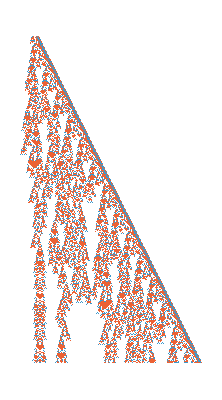
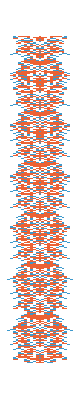
-Graphics--Graphics--Graphics-

```mathematica
Function[init, Row[Join[{ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[init, 3], 0}, 500], ImageSize->{Automatic, 300}, ColorRules->"Colors"]}, Labeled[ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[#Canonical, 3], 0}, 500], ImageSize->{Automatic, 300}, ColorRules->"Colors"], Text[#Period]]&/@DetectPeriod[{1329,{3,1},1},IntegerDigits[init, 3], 100]]]][166426]
```

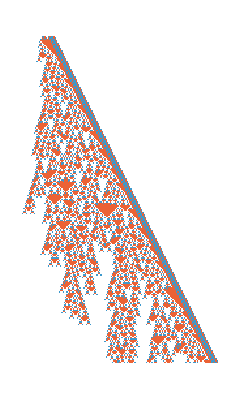
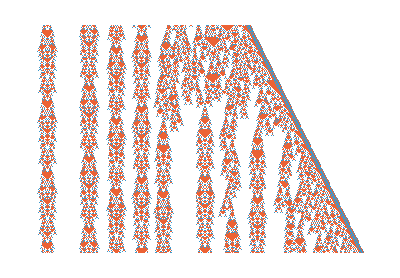
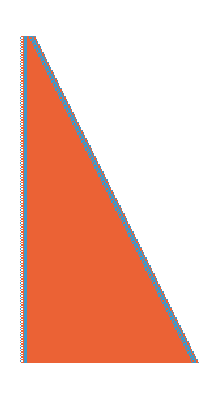
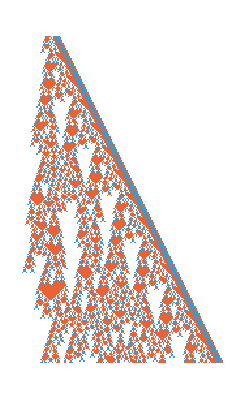
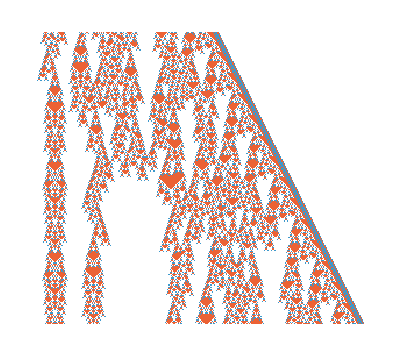
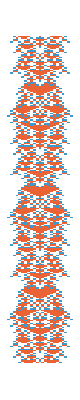
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics--Graphics-

```mathematica
Column[Function[init, Row[Join[{ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[init, 3], 0}, 250], ImageSize->{Automatic, 300}, ColorRules->"Colors"]}, Labeled[ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[#Canonical, 3], 0}, 250], ImageSize->{Automatic, 300}, ColorRules->"Colors"], Text[#Period]]&/@DetectPeriod[{1329,{3,1},1},IntegerDigits[init, 3], 100]]]]/@ {54889,97439,166426}]
```

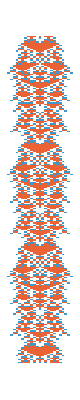
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics-

```mathematica
Column[Function[init, Row[Join[{ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[init, 3], 0}, 250], ImageSize->{Automatic, 300}, ColorRules->"Colors"]}, Labeled[ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[#Canonical, 3], 0}, 250], ImageSize->{Automatic, 300}, ColorRules->"Colors"], Text[#Period]]&/@DetectPeriod[{1329,{3,1},1},IntegerDigits[init, 3], 100]]]]/@ {54889,97439,166426}]
```

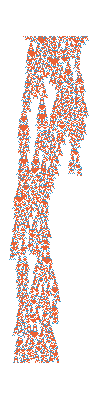
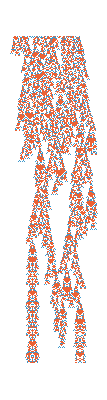
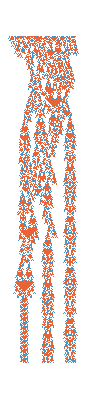
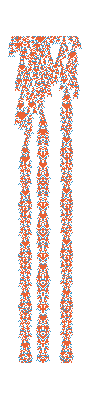
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
SeedRandom[452535];Function[init, GraphicsRow[Join[{ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[init, 3], 0}, 500], ImageSize->{Automatic, 300}, ColorRules->"Colors"]}, Labeled[ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[#Canonical, 3], 0}, 500], ImageSize->{Automatic, 300}, ColorRules->"Colors"], Text[#Period]]&/@DetectPeriod[{1329,{3,1},1},IntegerDigits[init, 3], 100, 10]], Frame->True]]/@ (FromDigits[#, 3]&/@ RandomInteger[3, {10, 100}])
```

```mathematica
SeedRandom[452535];DetectPeriod[{1329,{3,1},1},IntegerDigits[#, 3], 100]&/@ (FromDigits[#, 3]&/@ RandomInteger[3, {10, 100}])
```

{{},{<|Period→0,Canonical→1008811062,Shift→0,IsGliderGun→True|>},{<|Period→7,Canonical→22960,Shift→-Log[3653647/154980]/Log[3]|>},{},{},{<|Period→0,Canonical→4397453362786617132170805,Shift→0,IsGliderGun→True|>,<|Period→0,Canonical→3217566375,Shift→0,IsGliderGun→True|>},{},{},{},{}}

```mathematica
SeedRandom[452535]; FromDigits[RandomInteger[3, {10, 100}][[5]], 3]
```

542470711603459723256196960924563052255603464220

```mathematica
DetectPeriod[{1329,{3,1},1},IntegerDigits[542470711603459723256196960924563052255603464220, 3], 100]
```

{<|Period→78,Canonical→9571,Shift→0|>,<|Period→78,Canonical→9571,Shift→0|>}

```mathematica
GraphicsRow[Labeled[RulePlot[CellularAutomaton[{1329,{3,1},1}],CenterArray[IntegerDigits[#[[1]],3],500],250,PlotRange->{Automatic,#[[2]]},ImageSize->{Automatic,500}],Text[Style[ToString[#[[1]]]<>"\n"<>#[[3]],Italic,TextAlignment->Center]],ImageSize->{Automatic,530}]&/@{{1,{235,265},"(period 78)"},{52,{235,265},"(period 7)"},{400,{235,265},"(period 2)"},{800,{235,265},"(period 12)"},{916,{230,290},"(period 31R)"},{2617,{220,280},"(period 9)"},{2669,{230,290},"(period 48R)"},{97357,{235,265},"(period 2)"},{659197,{235,265},"(period 9)"}},ImageSize->{Automatic,610}]
```

```mathematica
SeedRandom[452535];Function[init, GraphicsRow[Join[{ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[init, 3], 0}, 1000], ImageSize->{Automatic, 300}, ColorRules->"Colors"]}, Labeled[ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[#Canonical, 3], 0}, 2#Period], ImageSize->{Automatic, 300}, ColorRules->"Colors"], Text[#Period]]&/@DetectPeriod[{1329,{3,1},1},IntegerDigits[init, 3], 100, 10]], Frame->True]]/@ (FromDigits[#, 3]&/@ RandomInteger[3, {50, 100}])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Parallel
```

```mathematica
SeedRandom[452535];Function[init, GraphicsRow[Join[{ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[init, 3], 0}, 500], ImageSize->{Automatic, 300}, ColorRules->"Colors"]}, Labeled[ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[#Canonical, 3], 0}, 500], ImageSize->{Automatic, 300}, ColorRules->"Colors"], Text[#Period]]&/@DetectPeriod[{1329,{3,1},1},IntegerDigits[init, 3], 100, 10]], Frame->True]]/@ (FromDigits[#, 3]&/@ RandomInteger[3, {50, 50}])
```

```mathematica
(* Find all solutions with periods that aren't easy to find *)
numtosearch=100;
initwidth=100;
easysolutionperiods={78};  (* include 9 and 22, then 4 and 38 for longer searches *)

rand  = RandomInteger[{0, 2}, {numtosearch, initwidth}]; 
easysolutionperiods=Dispatch[Append[#->True&/@easysolutionperiods, _->False]];
foundraw = Table[DetectPeriod[{1329,{3,1},1}, i][[All, "Period"]], {i, rand}];
foundbool = Map[#/.easysolutionperiods&, foundraw, {2}];
(*found=Table[If[AllTrue[DetectPeriod[{1329,{3,1},1}, #][[All, "Period"]], elem|->elem/.easysolutionperiods],Nothing,#]&[RandomInteger[{0, 2}, initwidth]], {i, numtosearch}];
foundbool = Table[#/.easysolutionperiods&/@DetectPeriod[{1329,{3,1},1}, #][[All, "Period"]]&[RandomInteger[{0, 2}, initwidth]], {i, numtosearch}];*)
Table[
Labeled[ArrayPlot[CellularAutomaton[{1329,{3,1},1}, {sol, 0}, 200]], ClickToCopy[Values@DetectPeriod[{1329,{3,1},1}, sol], sol]],{sol, found}]
```

First::normal: Nonatomic expression expected at position 1 in First[0].

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
foundraw
```

{{},{78,78,78},{78,78,78},{78},{78,78},{78,78},{0},{78,78,78},{78,78,78},{78},{78,78},{78},{78,78,78},{78,78},{78,78},{0,78,78},{78},{78,78},{78,78},{78},{0,0},{78},{78,78},{78,78,78},{78,78,78},{0,78},{78,78},{7,78,78},{78,78,48,78,78},{78,78,78},{78,0,0},{78,78,78},{9},{},{0},{78},{78,78},{78,78},{12,78,78,78},{78,78},{78,78,78},{0},{78,78,78},{78},{78,78,78,78},{78},{0,78,78},{78,78},{78},{78,78},{7},{78,78},{78,78,78},{78,0},{78,78},{78,78},{78,78},{78,78},{78,78},{78,78},{0,78,78,78},{78,78},{78},{78,78,78},{78},{31,78},{0,0,78},{78,78},{7},{78,78},{78},{0,78,78},{78,78},{78,0,0},{78,78,78},{78,78,78},{78,78},{78,0},{78,78,78},{78,78},{78},{78,78,78},{78,78},{78,78},{78,78},{78,78,78,78},{78},{78,7,78},{78},{78},{0},{78},{78,78},{78,78},{78,78},{78,78,78},{78,78},{78,78,78},{78},{78}}

```mathematica
foundbool
```

{{},{True,True,True},{True,True,True},{True},{True,True},{True,True},{False},{True,True,True},{True,True,True},{True},{True,True},{True},{True,True,True},{True,True},{True,True},{False,True,True},{True},{True,True},{True,True},{True},{False,False},{True},{True,True},{True,True,True},{True,True,True},{False,True},{True,True},{False,True,True},{True,True,False,True,True},{True,True,True},{True,False,False},{True,True,True},{False},{},{False},{True},{True,True},{True,True},{False,True,True,True},{True,True},{True,True,True},{False},{True,True,True},{True},{True,True,True,True},{True},{False,True,True},{True,True},{True},{True,True},{False},{True,True},{True,True,True},{True,False},{True,True},{True,True},{True,True},{True,True},{True,True},{True,True},{False,True,True,True},{True,True},{True},{True,True,True},{True},{False,True},{False,False,True},{True,True},{False},{True,True},{True},{False,True,True},{True,True},{True,False,False},{True,True,True},{True,True,True},{True,True},{True,False},{True,True,True},{True,True},{True},{True,True,True},{True,True},{True,True},{True,True},{True,True,True,True},{True},{True,False,True},{True},{True},{False},{True},{True,True},{True,True},{True,True},{True,True,True},{True,True},{True,True,True},{True},{True}}

```mathematica
found[[1]]
```

{2,0,1,0,1,2,0,2,0,1,0,0,1,2,0,1,1,1,1,0,1,1,0,1,0,0,1,2,0,1,0,0,0,0,0,1,1,2,1,2,0,0,0,2,2,0,0,1,2,1,0,1,0,2,1,2,1,0,0,2,1,1,2,1,0,0,2,1,0,0,1,1,2,1,0,1,2,0,2,2,1,1,1,2,1,1,2,1,2,2,0,1,1,0,1,2,0,1,0,2}

```mathematica
Function[init, GraphicsRow[Join[{ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[init, 3], 0}, 1000], ImageSize->{Automatic, 300}, ColorRules->"Colors"]}, Labeled[ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[#Canonical, 3], 0}, 4#Period], ImageSize->{Automatic, 300}, ColorRules->"Colors"], Text[#Period]]&/@DetectPeriod[{1329,{3,1},1},IntegerDigits[init, 3], 100, 10]], Frame->True]]/@ (foundraw[[;;3]])
```

```mathematica
Function[init, GraphicsRow[Join[{ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[init, 3], 0}, 1000], ImageSize->{Automatic, 300}, ColorRules->"Colors"]}, Labeled[ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[#Canonical, 3], 0}, 4#Period], ImageSize->{Automatic, 300}, ColorRules->"Colors"], Text[#Period]]&/@DetectPeriod[{1329,{3,1},1},IntegerDigits[init, 3], 100, 10]], Frame->True]]/@ (FromDigits[#, 3]&/@ found)
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* Find all solutions with periods that aren't easy to find *)
numtosearch=100;
initwidth=100;
easysolutionperiods={78};  (* include 9 and 22, then 4 and 38 for longer searches *)
```

```mathematica
rand  = RandomInteger[{0, 2}, {numtosearch, initwidth}];
```

```mathematica
easysolutionperiods=Dispatch[Append[#->True&/@easysolutionperiods, _->False]];
```

```mathematica
all2 = Table[DetectPeriod[{1329,{3,1},1}, i], {i, rand}];
```

```mathematica
all = Quiet[Table[DetectPeriod[{1329,{3,1},1}, i, 100, 10][[All, "Period"]], {i, rand}]];
```

```mathematica
found = rand[[Select[Range[Length[rand]],!AllTrue[all[[#]], elem|->elem/. easysolutionperiods]&]]];
```

```mathematica
Select[Range[Length[rand]],!AllTrue[all[[#]], elem|->elem/. easysolutionperiods]&]
```

{7,9,10,15,17,18,19,21,22,26,28,31,35,38,44,45,46,48,49,52,57,60,63,68,75,77,81,84,85,94,95,98,99}

```mathematica
all
```

{{78,78,78,78},{78,78},{78,78,78},{78},{78,78},{78,78},{0,0,0},{78},{0},{78,12},{78},{78,78,78},{78},{78,78},{7,78},{78},{31,78,78},{78,0},{7,78},{78},{0,78,78},{0},{78,78},{78,78},{78,78,78},{7,78},{},{0},{78,78},{78,78,78},{0,78,78},{78,78},{78,78},{},{78,0,78},{78},{78,78,78},{78,7,0},{78},{78},{78,78,78},{78,78},{78,78},{0},{78,0,78},{78,78,0},{78,78,78},{7,78},{7,78},{78},{78,78},{78,48,78,78,78},{78,78},{78,78},{78,78},{78,78},{0,78},{78,78},{78,78,78},{0,78,78},{78,78,78},{78,78},{12,0,78},{78},{78},{78,78},{},{7,78,78,78},{78,78},{78},{78},{},{78,78},{78},{0,0},{78,78,78},{7,78},{},{78,78},{78,78},{0,0},{78},{78,78,78},{0},{0,0,78},{78,78},{78,78},{78,78,78},{78,78,78},{78,78},{78,78,78},{78,78},{78,78},{0},{0,78},{78},{},{9,78},{0,78},{78}}

```mathematica
all2[[7]]
```

{<|Period→0,Canonical→5961912496915332227854860,Shift→0,IsGliderGun→True|>,<|Period→0,Canonical→162868643066171004895215,Shift→0,IsGliderGun→True|>,<|Period→0,Canonical→1591191324,Shift→0,IsGliderGun→True|>}

```mathematica
rand[[7]]
```

{0,1,2,2,0,2,2,0,0,2,0,1,0,1,2,2,1,2,0,0,1,1,2,0,2,1,2,2,2,1,2,1,2,2,2,1,2,2,0,1,2,0,1,2,1,1,2,1,2,2,1,2,1,2,1,2,2,0,1,2,1,1,1,0,1,1,2,1,2,2,1,2,1,2,2,2,1,2,2,2,2,2,0,0,0,0,2,1,1,2,2,2,0,1,0,2,1,2,2,0}

```mathematica
ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {rand[[7]], 0}, 1000], ImageSize->{Automatic, 300}, ColorRules->"Colors"]
```

-Graphics-

```mathematica
DetectPeriod[{1329,{3,1},1},rand[[7]], 100, 10]
```

{<|Period→78,Canonical→9571,Shift→0|>,<|Period→78,Canonical→9571,Shift→0|>,<|Period→78,Canonical→9571,Shift→0|>}

```mathematica
Function[init, GraphicsRow[Join[{ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[init, 3], 0}, 1000], ImageSize->{Automatic, 300}, ColorRules->"Colors"]}, Labeled[ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[#Canonical, 3], 0}, 4#Period], ImageSize->{Automatic, 300}, ColorRules->"Colors"], Text[#Period]]&/@DetectPeriod[{1329,{3,1},1},IntegerDigits[init, 3], 100, 10]], Frame->True]]/@ (FromDigits[#, 3]&/@ found[[;;3]])
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* Find all solutions with periods that aren't easy to find *)
SeedRandom[325212411];
numtosearch=10000;
initwidth=100;
easysolutionperiods={78, 7};  (* include 9 and 22, then 4 and 38 for longer searches *)
rand  = RandomInteger[{0, 2}, {numtosearch, initwidth}]; 
easysolutionperiods=Dispatch[Append[#->True&/@easysolutionperiods, _->False]];
all = Quiet[ParallelTable[DetectPeriod[{1329,{3,1},1}, i, 100, 10][[All, "Period"]], {i, rand}]];
found = rand[[Select[Range[Length[rand]],!AllTrue[all[[#]], elem|->elem/. easysolutionperiods]&]]];
```

First::normal: Nonatomic expression expected at position 1 in First[0].

General::stop: Further output of First::normal will be suppressed during this calculation.

```mathematica
Length[found]
```

771

```mathematica
KeySort[Counts[Catenate[all]]]
```

<|0→160,7→948,9→57,12→356,31→178,35→2,48→104,78→20152,156→5|>

```mathematica
Select[all,MemberQ[#, 156]&->"Index"]
```

{1181,4585,4693,6196,7050}

```mathematica
rand[[1181]]
```

{1,0,0,0,0,1,1,2,0,1,2,2,2,0,2,0,2,2,2,1,0,1,1,0,2,0,0,0,0,2,0,1,1,2,1,0,2,0,1,2,2,2,1,0,0,1,2,2,1,2,1,1,1,2,2,2,0,2,2,2,2,2,2,0,1,1,1,2,2,0,2,2,0,1,0,2,0,0,0,1,2,1,1,1,0,0,0,2,2,0,1,2,0,2,0,0,2,1,2,1}

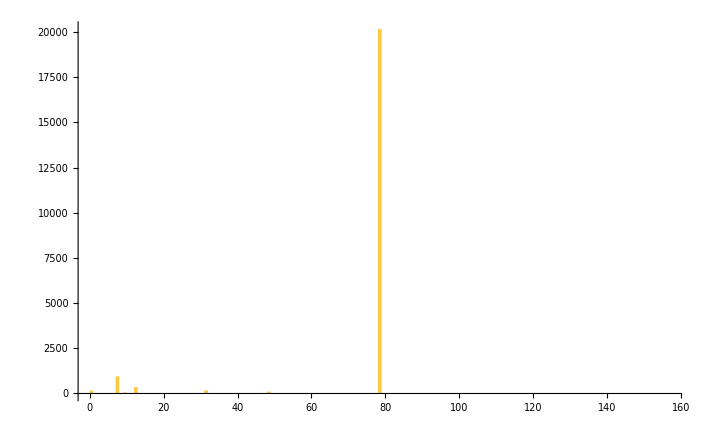

```mathematica
Histogram[Catenate[all], {1}]
```

```mathematica
Histogram[found[[All, ]]]
```

```mathematica
ParallelMap[Function[init, GraphicsRow[Join[{ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[init, 3], 0}, 1000], ImageSize->{Automatic, 300}, ColorRules->"Colors"]}, Labeled[ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[#Canonical, 3], 0}, 4#Period], ImageSize->{Automatic, 300}, ColorRules->"Colors"], Text[#Period]]&/@DetectPeriod[{1329,{3,1},1},IntegerDigits[init, 3], 100, 10]], Frame->True]], (FromDigits[#, 3]&/@ found[[;;100]])]
```

First::normal: Nonatomic expression expected at position 1 in First[0].

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
SeedRandom[2053302958035839];
numtosearch=10000;
initwidth=100;
easysolutionperiods={78, 7};  (* include 9 and 22, then 4 and 38 for longer searches *)
rand  = RandomInteger[{0, 2}, {numtosearch, initwidth}]; 
easysolutionperiods=Dispatch[Append[#->True&/@easysolutionperiods, _->False]];
all = Quiet[ParallelTable[DetectPeriod[{1329,{3,1},1}, i, 100, 15][[All, "Period"]], {i, rand}]];
found = rand[[Select[Range[Length[rand]],!AllTrue[all[[#]], elem|->elem/. easysolutionperiods]&]]];
```

First::normal: Nonatomic expression expected at position 1 in First[0].

General::stop: Further output of First::normal will be suppressed during this calculation.

```mathematica
KeySort[Counts[Catenate[all]]]
```

<|0→9,2→5,7→893,9→47,12→357,31→186,35→3,48→120,78→20150,156→1,234→1|>

```mathematica
Factor[234]
```

234

```mathematica
Divisors[234]
```

{1,2,3,6,9,13,18,26,39,78,117,234}

```mathematica
234/78
```

3

```mathematica
Select[all,MemberQ[#, 234]&->"Index"]
```

{8798}

```mathematica
Function[init, GraphicsRow[Join[{ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[init, 3], 0}, 1000], ImageSize->{Automatic, 300}, ColorRules->"Colors"]}, Labeled[ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[#Canonical, 3], 0}, 4#Period], ImageSize->{Automatic, 300}, ColorRules->"Colors"], Text[#Period]]&/@DetectPeriod[{1329,{3,1},1},IntegerDigits[init, 3], 100, 10]], Frame->True]]/@(FromDigits[#, 3]&/@ rand[[{8798}]])
```

{-Graphics-}

```mathematica
rand[[Select[all, MemberQ[#, 0]&->"Index"]]]
```

{{1,2,2,0,2,0,2,0,0,0,1,2,2,1,0,0,0,2,0,2,2,0,1,0,1,0,1,2,1,0,1,2,1,2,1,0,0,0,2,1,0,1,2,1,0,0,2,2,1,2,0,1,2,2,0,2,0,0,1,2,2,2,2,1,0,2,0,2,2,0,1,0,0,2,1,1,2,1,1,1,2,0,2,1,0,0,1,0,1,1,2,1,2,1,0,1,2,2,2,0},{2,0,0,0,1,2,2,1,2,1,0,0,0,0,2,2,2,0,1,2,1,2,1,2,1,1,2,2,1,2,2,0,0,1,0,2,0,1,2,2,2,0,2,2,1,1,0,0,2,0,1,0,1,1,2,2,2,0,2,0,0,1,1,1,1,2,2,0,0,2,2,2,2,0,2,0,2,1,0,2,0,1,1,0,2,0,2,2,1,2,0,2,0,2,2,2,0,2,2,1},{1,1,2,0,1,1,0,0,2,2,2,0,2,0,0,2,1,0,1,2,2,2,2,2,0,2,0,0,0,2,2,1,0,1,1,1,1,1,1,2,1,0,1,1,0,2,2,0,2,2,2,1,1,0,0,1,0,0,1,1,1,0,1,0,0,2,2,1,1,2,2,2,0,0,1,2,1,2,0,1,2,1,1,2,0,0,2,2,1,1,1,0,0,2,1,0,0,2,1,0},{0,0,2,0,0,0,1,2,0,0,2,2,1,1,2,2,2,1,0,2,0,1,2,2,0,0,2,0,2,2,0,2,0,0,1,0,2,0,1,2,0,2,2,0,0,1,2,2,2,2,0,2,1,0,2,1,0,1,1,2,0,2,1,0,0,2,2,1,0,0,0,1,1,1,0,2,0,2,0,2,2,0,0,0,2,2,2,2,1,0,1,2,0,2,0,0,2,1,0,1},{1,0,2,0,0,1,2,1,0,2,0,2,1,0,0,1,1,1,2,0,1,2,1,0,0,2,1,2,1,1,0,0,0,2,0,2,2,0,0,2,2,2,1,1,2,1,2,0,1,1,1,1,0,0,1,0,1,1,1,0,0,0,0,2,2,0,0,1,0,2,0,0,1,2,2,1,1,2,0,0,0,2,0,1,1,0,0,1,2,2,2,0,0,2,0,0,0,1,0,0},{1,0,0,0,2,2,0,2,2,0,1,0,0,0,1,1,1,2,2,1,0,1,2,0,1,2,1,0,2,2,0,0,0,0,2,2,2,0,0,0,1,1,0,1,1,0,0,1,2,1,2,1,2,0,2,2,2,0,2,1,1,1,0,0,1,0,0,2,0,0,2,1,2,1,1,1,1,0,2,2,2,0,1,2,1,1,1,1,0,0,1,0,0,1,2,1,2,2,1,0},{1,2,1,0,0,1,0,2,0,0,0,2,1,0,1,1,0,1,1,0,1,0,2,1,0,0,2,0,2,1,0,1,1,1,2,2,2,0,0,2,1,1,0,2,1,2,0,0,0,2,0,2,0,2,1,2,0,1,0,2,2,2,2,1,0,1,2,2,0,1,0,2,2,0,1,1,1,2,1,1,1,1,1,0,0,0,1,1,2,1,0,0,1,1,2,1,0,2,1,1},{0,0,2,1,2,1,0,2,2,2,1,0,1,0,1,2,0,1,2,1,0,1,1,1,2,2,2,2,2,2,1,1,1,1,1,0,2,2,0,0,2,1,0,0,0,1,0,0,2,2,2,2,2,0,1,0,2,0,0,1,0,1,1,0,0,0,1,1,2,2,2,0,1,0,2,0,0,1,2,2,0,1,2,0,1,2,2,1,1,0,2,0,1,1,2,0,2,0,2,1}}

```mathematica
ParallelMap[Function[init, GraphicsRow[Join[{ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[init, 3], 0}, 1000], ImageSize->Automatic, ColorRules->"Colors"]}, Labeled[ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[#Canonical, 3], 0}, 4#Period], ImageSize->{Automatic, 300}, ColorRules->"Colors"], Text[#Period]]&/@DetectPeriod[{1329,{3,1},1},IntegerDigits[init, 3], 100, 10]], Frame->True]], (FromDigits[#, 3]&/@ found[[;;100]])]
```

First::normal: Nonatomic expression expected at position 1 in First[0].

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelMap[Function[init, GraphicsRow[Join[{ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[init, 3], 0}, 2000], ImageSize->Automatic, ColorRules->"Colors"]}, Labeled[ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[#Canonical, 3], 0}, 4#Period], ImageSize->Automatic, ColorRules->"Colors"], Text[#Period]]&/@DetectPeriod[{1329,{3,1},1},IntegerDigits[init, 3], 100, 10]], Frame->True]], (FromDigits[#, 3]&/@ rand[[Select[all, MemberQ[#, 0]&->"Index"]]])]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Function[init, GraphicsRow[Join[{ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[init, 3], 0}, 1000], ImageSize->{Automatic, 300}, ColorRules->"Colors"]}, Labeled[ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[#Canonical, 3], 0}, 4#Period], ImageSize->{Automatic, 300}, ColorRules->"Colors"], Text[#Period]]&/@DetectPeriod[{1329,{3,1},1},IntegerDigits[init, 3], 100, 10]], Frame->True]][(FromDigits[#, 3]&[rand[[1181]]])]
```

-Graphics-

```mathematica
rand[[1181]]
```

## Todo

### Make sure DetectPeriod is working properly with different radius values

```mathematica
Function[init, GraphicsRow[Join[{ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[init, 3], 0}, 1000], ImageSize->{Automatic, 300}, ColorRules->"Colors"]}, Labeled[ArrayPlot[CellularAutomaton[{1329,{3,1},1} , {IntegerDigits[#Canonical, 3], 0}, 4#Period], ImageSize->{Automatic, 300}, ColorRules->"Colors"], Text[#Period]]&/@DetectPeriod[{1329,{3,1},1},IntegerDigits[init, 3], 100, 10]], Frame->True]][(FromDigits[#, 3]&[{1,0,0,0,0,1,1,2,0,1,2,2,2,0,2,0,2,2,2,1,0,1,1,0,2,0,0,0,0,2,0,1,1,2,1,0,2,0,1,2,2,2,1,0,0,1,2,2,1,2,1,1,1,2,2,2,0,2,2,2,2,2,2,0,1,1,1,2,2,0,2,2,0,1,0,2,0,0,0,1,2,1,1,1,0,0,0,2,2,0,1,2,0,2,0,0,2,1,2,1}])]
```

## Long run

```mathematica
(* Find all solutions with periods that aren't easy to find *)
numtosearch=1000000;
initwidth=300;
easysolutionperiods={0, 1, 2, 4, 9,  38, 22};  (* include 9 and 22, then 4 and 38 for longer searches *)


easysolutionperiods=Dispatch[Append[#->True&/@easysolutionperiods, _->False]];

found=ParallelTable[If[AllTrue[DetectPeriod[{20, {2, 1}, 2}, #][[All, "Period"]], elem|->elem/.easysolutionperiods],Nothing,#]&[RandomInteger[{0, 1}, initwidth]], {i, numtosearch}];

ParallelTable[
Labeled[ArrayPlot[CellularAutomaton[{20, {2, 1}, 2}, {sol, 0}, 200]], ClickToCopy[Values@DetectPeriod[{20, {2, 1}, 2}, sol], sol]],{sol, found}]
```

{-Graphics-,-Graphics-}

```mathematica
CloudConnect["wnielsen@wolframinstitute.org"]
```

wnielsen@wolframinstitute.org

```mathematica
SeedRandom[325235325 + i];
```

```mathematica
RemoteBatchSubmit[
Module[{numtosearch=100000,
initwidth=50,
easysolutionperiods={0, 1, 2, 4, 9,  38, 22}},
easysolutionperiods=Dispatch[Append[#->True&/@easysolutionperiods, _->False]];ParallelTable[SeedRandom[325235325 + i];If[AllTrue[DetectPeriod[{20, {2, 1}, 2}, #][[All, "Period"]], elem|->elem/.easysolutionperiods],Nothing,#]&[IntegerDigits[i, 2,initwidth]], {i, numtosearch}]], CreditConstraint->5000, RemoteMachineClass->"Compute192x384"]
```

RemoteBatchJobObject[…]

```mathematica
RemoteBatchJobObject[…]["JobStatus"]
```

Queued

```mathematica
RemoteBatchSubmit[Module[{numtosearch=100000,
initwidth=50,
easysolutionperiods={0, 1, 2, 4, 9,  38, 22}},
easysolutionperiods=Dispatch[Append[#->True&/@easysolutionperiods, _->False]];ParallelTable[SeedRandom[325235325 + i];If[AllTrue[DetectPeriod[{20, {2, 1}, 2}, #][[All, "Period"]], elem|->elem/.easysolutionperiods],Nothing,#]&[IntegerDigits[i, 2,initwidth]], {i, numtosearch}]], CreditConstraint->5000, RemoteMachineClass->"Compute64x128"]
```

RemoteBatchJobObject[…]

```mathematica
RemoteBatchSubmit[Module[{numtosearch=100000,
initwidth=50,
easysolutionperiods={0, 1, 2, 4, 9,  38, 22}},
easysolutionperiods=Dispatch[Append[#->True&/@easysolutionperiods, _->False]];ParallelTable[SeedRandom[325235325 + i];If[AllTrue[DetectPeriod[{20, {2, 1}, 2}, #][[All, "Period"]], elem|->elem/.easysolutionperiods],Nothing,#]&[IntegerDigits[i, 2,initwidth]], {i, numtosearch}]], CreditConstraint->5000, RemoteMachineClass->"Memory192x1536"]
```

RemoteBatchJobObject[…]

```mathematica
RemoteBatchSubmit[Module[{numtosearch=100000,
initwidth=50,
easysolutionperiods={0, 1, 2, 4, 9,  38, 22}},
easysolutionperiods=Dispatch[Append[#->True&/@easysolutionperiods, _->False]];ParallelTable[SeedRandom[325235325 + i];If[AllTrue[DetectPeriod[{20, {2, 1}, 2}, #][[All, "Period"]], elem|->elem/.easysolutionperiods],Nothing,#]&[IntegerDigits[i, 2,initwidth]], {i, numtosearch}]], CreditConstraint->5000, RemoteMachineClass->"Memory16x128"]
```

RemoteBatchJobObject[…]

```mathematica
jobs1 ={ RemoteBatchJobObject[…],RemoteBatchJobObject[…],RemoteBatchJobObject[…],RemoteBatchJobObject[…]};
```

```mathematica
#["EvaluationResult"]&/@ jobs1
```

```mathematica
[[1]]//Length
```

100000

```mathematica
CloudConnect["wnielsen@wolframinstitute.org"]
```

wnielsen@wolframinstitute.org

!!! This costs money !!!

```mathematica
(*jobs = RemoteBatchSubmit[
Module[{numtosearch=1000000,
initwidth=50,
easysolutionperiods={0, 1, 2, 4, 9,  38, 22}},
easysolutionperiods=Dispatch[Append[#->True&/@easysolutionperiods, _->False]];ParallelTable[SeedRandom[325235325 + i];If[AllTrue[DetectPeriod[{20, {2, 1}, 2}, #][[All, "Period"]], elem|->elem/.easysolutionperiods],Nothing,#]&[IntegerDigits[i, 2,initwidth]], {i, numtosearch}]], CreditConstraint->5000, RemoteMachineClass->#]&/@ {"Compute192x384", "Compute64x128", "Memory192x1536", "Memory16x128"};*)
```

```mathematica
RemoteBatchSubmit[
Module[{numtosearch=1000000,
initwidth=50,
easysolutionperiods={0, 1, 2, 4, 9,  38, 22}},
easysolutionperiods=Dispatch[Append[#->True&/@easysolutionperiods, _->False]];ParallelTable[SeedRandom[325235325 + i];If[AllTrue[DetectPeriod[{20, {2, 1}, 2}, #][[All, "Period"]], elem|->elem/.easysolutionperiods],Nothing,#]&[IntegerDigits[i, 2,initwidth]], {i, numtosearch}]], CreditConstraint->5000, RemoteMachineClass->"Compute192x384"]
```

```mathematica
RemoteBatchSubmit[Module[{numtosearch=1000000,
initwidth=50,
easysolutionperiods={0, 1, 2, 4, 9,  38, 22}},
easysolutionperiods=Dispatch[Append[#->True&/@easysolutionperiods, _->False]];ParallelTable[SeedRandom[325235325 + i];If[AllTrue[DetectPeriod[{20, {2, 1}, 2}, #][[All, "Period"]], elem|->elem/.easysolutionperiods],Nothing,#]&[IntegerDigits[i, 2,initwidth]], {i, numtosearch}]], CreditConstraint->5000, RemoteMachineClass->"Compute64x128"]
```

```mathematica
RemoteBatchSubmit[Module[{numtosearch=1000000,
initwidth=50,
easysolutionperiods={0, 1, 2, 4, 9,  38, 22}},
easysolutionperiods=Dispatch[Append[#->True&/@easysolutionperiods, _->False]];ParallelTable[SeedRandom[325235325 + i];If[AllTrue[DetectPeriod[{20, {2, 1}, 2}, #][[All, "Period"]], elem|->elem/.easysolutionperiods],Nothing,#]&[IntegerDigits[i, 2,initwidth]], {i, numtosearch}]], CreditConstraint->5000, RemoteMachineClass->"Memory192x1536"]
```

```mathematica
RemoteBatchSubmit[Module[{numtosearch=1000000,
initwidth=50,
easysolutionperiods={0, 1, 2, 4, 9,  38, 22}},
easysolutionperiods=Dispatch[Append[#->True&/@easysolutionperiods, _->False]];ParallelTable[SeedRandom[325235325 + i];If[AllTrue[DetectPeriod[{20, {2, 1}, 2}, #][[All, "Period"]], elem|->elem/.easysolutionperiods],Nothing,#]&[IntegerDigits[i, 2,initwidth]], {i, numtosearch}]], CreditConstraint->5000, RemoteMachineClass->"Memory16x128"]
```

## LR2

```mathematica
DetectPeriod[{1329,{3,1},1}, IntegerDigits[028149, 2], 100, 15]
```

{<|Period→78,Canonical→9571,Shift→0|>}

```mathematica
SeedRandom[2053302958035839];
numtosearch=100;
initwidth=100;
easysolutionperiods={78, 7};  (* include 9 and 22, then 4 and 38 for longer searches *)
rand  = RandomInteger[{0, 2}, {numtosearch, initwidth}]; 
easysolutionperiods=Dispatch[Append[#->True&/@easysolutionperiods, _->False]];
all = Quiet[ParallelTable[Join[<|"InitialCondition"->i|>, #]&/@DetectPeriod[{1329,{3,1},1}, i, 100, 15], {i, rand}]];
found = rand[[Select[Range[Length[rand]],!AllTrue[all[[#]], elem|->elem/. easysolutionperiods]&]]];
```

```mathematica
all = DetectPeriod[{1329,{3,1},1}, i, 100, 15]
```

```mathematica
Select[all,!AllTrue[all[[#]], elem|->elem/. easysolutionperiods]&->"Index"]
```

```mathematica
jobs = RemoteBatchSubmit[
Module[{numtosearch=1000000,
initwidth=50,
easysolutionperiods={0, 1, 2, 4, 9,  38, 22}},
easysolutionperiods=Dispatch[Append[#->True&/@easysolutionperiods, _->False]];ParallelTable[SeedRandom[325235325 + i];If[AllTrue[DetectPeriod[{20, {2, 1}, 2}, #][[All, "Period"]], elem|->elem/.easysolutionperiods],Nothing,#]&[IntegerDigits[i, 2,initwidth]], {i, numtosearch}]], CreditConstraint->5000, RemoteMachineClass->#]&/@ {"Compute192x384", "Compute64x128", "Memory192x1536", "Memory16x128"}
```

```mathematica
jobs = RemoteBatchSubmit[
Module[{numtosearch=1000000,
initwidth=50,
easysolutionperiods={0, 1, 2, 4, 9,  38, 22}},
easysolutionperiods=Dispatch[Append[#->True&/@easysolutionperiods, _->False]];ParallelTable[SeedRandom[325235325 + i];If[AllTrue[DetectPeriod[{20, {2, 1}, 2}, #][[All, "Period"]], elem|->elem/.easysolutionperiods],Nothing,#]&[IntegerDigits[i, 2,initwidth]], {i, numtosearch}]], CreditConstraint->5000, RemoteMachineClass->#]&/@ {"Compute192x384", "Compute64x128", "Memory192x1536", "Memory16x128"}
```

```mathematica
jobs = RemoteBatchSubmit[Module[{numtosearch=1000000,
initwidth=50,
easysolutionperiods={0, 1, 2, 4, 9,  38, 22}},
easysolutionperiods=Dispatch[Append[#->True&/@easysolutionperiods, _->False]];ParallelTable[SeedRandom[325235325 + i];If[AllTrue[DetectPeriod[{20, {2, 1}, 2}, #][[All, "Period"]], elem|->elem/.easysolutionperiods],Nothing,#]&[IntegerDigits[i, 2,initwidth]], {i, numtosearch}]], CreditConstraint->5000, RemoteMachineClass->#]&/@ {"Compute192x384", "Compute64x128", "Memory192x1536", "Memory16x128"}
```